```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\Dokumente\Dissertation\Papers\paper-2021-summaryvis-storytelling

```mathematica
replaceFaulty[l_List,err_]:=Module[{split,first},
split=Partition[SplitBy[l,#==err&]/.{e:1err..}:>Length[{e}],UpTo[3],1]/.{
{i1_Integer,l1_List,i2_Integer}:>{Table[First@l1,{i1}]},
{l1_List,i_Integer}:>{Join[l1,Table[Last@l1,{i}]]},
{l1_List,i_Integer,l2_List}:>{Join[l1,Table[(Last@l1+First@l2)/2,{i}]]}
};
If[First@l===err,first=First@split;split=Drop[split,1],first={}];
Flatten@Prepend[split⟦;;;;2⟧,first]
]
```

```mathematica
starless=Import["starless.wav"];
(*starless=Import["comfortablynumb.wav"];*)
```

```mathematica
{left,right}=Audio/@AudioData[starless];
```

```mathematica
{mfccleft,mfccright}=Standardize@AudioLocalMeasurements[#,{"MFCC"(*,20,40,20,20000*)}
,PartitionGranularity->{Quantity[2000,"Milliseconds"],Quantity[1000,"Milliseconds"],1&}
]&/@{left,right};
```

```mathematica
{featuresleft,featuresright}=(Through[AudioLocalMeasurements[#,{"SpectralCentroid","SpectralCrest","SpectralFlatness","SpectralKurtosis","SpectralRollOff","SpectralSkewness","SpectralSlope","SpectralSpread"},"List"
,PaddingSize->0
,PartitionGranularity->{Quantity[1000,"Milliseconds"],Quantity[1000,"Milliseconds"],1&}
]["Values"]])ᵀ&/@{left,right};
```

```mathematica
featuresleft⟦All,5⟧=replaceFaulty[featuresleft⟦All,5⟧,22049.50001133761];
featuresright⟦All,5⟧=replaceFaulty[featuresright⟦All,5⟧,22049.50001133761];
```

```mathematica
coords=DimensionReduce[mfccleft["Values"](*~Join~mfccright["Values"]*),2
,PerformanceGoal->"Quality"
,Method->{"TSNE","Perplexity"->50}];
(*coords=DimensionReduce[Transpose[Standardize/@Transpose[featuresleft~Join~featuresright]],2
,Method->{"TSNE","Perplexity"->300}
,PerformanceGoal->"Quality"];*)
(*coords=DimensionReduce[Transpose[Standardize/@Transpose[featuresleft]],2,Method->{"TSNE","Perplexity"->50}];*)
```

```mathematica
linedata=TimeSeries[#,Automatic,
ResamplingMethod->{"Interpolation",InterpolationOrder->2,Method->"Spline"}]&/@
Partition[Normal@coords,(*Length@featuresleft*)mfccleft["PathLength"]];
```

```mathematica
paths=((fun↦(fun/@Range[Sequence@@First[fun["Domain"]],0.1]))@#["PathFunction"])&/@linedata;
```

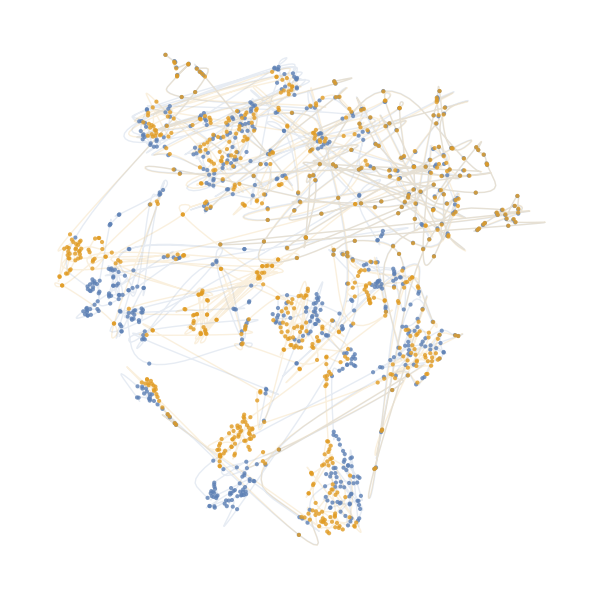

```mathematica
plot=ListPlot[Through@linedata@"Values"~Join~paths
,Joined->{False,False,True,True}
,PlotStyle->{
Directive[ColorData[97,1],AbsolutePointSize[3],Opacity[0.8]],
Directive[ColorData[97,2],AbsolutePointSize[3],Opacity[0.8]],
Directive[ColorData[97,1],AbsolutePointSize[0],AbsoluteThickness[1],Opacity[0.15]],
Directive[ColorData[97,2],AbsolutePointSize[0],AbsoluteThickness[1],Opacity[0.15]]
}
,PlotRange->All
,Axes->False
,AspectRatio->1
,ImageSize->600
]
```

```mathematica
SetEnvironment["PATH"->Environment["PATH"]<>";"<>"D:\\Dokumente\\Dissertation\\Code\\Python\\ptsne-pytorch\\env"]
```

```mathematica
SetEnvironment["PATH"->Environment["PATH"]<>";"<>"D:\\Dokumente\\Dissertation\\Code\\Python\\ptsne-pytorch\\env\\Library\\bin"]
```

```mathematica
RegisterExternalEvaluator["Python","D:\\Dokumente\\Dissertation\\Code\\Python\\ptsne-pytorch\\env\\python.exe"]
```

9ea5aca3-849b-4096-bf89-0e2a6ebac666

```mathematica
py=StartExternalSession["Python"]
```

ExternalSessionObject[…]

```mathematica
ExternalEvaluate[py,"from openTSNE import TSNE"]
```

```mathematica
tsne=ExternalFunction[py,"def DimensionReduce(data): return TSNE().fit(data)"]
```

ExternalFunction[…]

```mathematica
coords=tsne[mfccleft["Values"]~Join~mfccright["Values"]]
```

NumericArray[…]

```mathematica
edges=With[{len=Length@mfccleft["Values"]},
Join[
Style[#,Directive[ColorData[97,1],AbsoluteThickness[.8],Opacity[0.2]]]&/@UndirectedEdge@@@Partition[Range[len],2,1],
Style[#,Directive[ColorData[97,2],AbsoluteThickness[.8],Opacity[0.2]]]&/@UndirectedEdge@@@Partition[Range[len+1,2*Length@mfccleft["Values"]],2,1]]
];
```

```mathematica
gr=Graph[edges,VertexCoordinates->Normal[coords],
VertexStyle->Join[
Thread[Range[Length@edges/2]->Directive[ColorData[97,1],AbsolutePointSize[4],Opacity[0.6]]],
Thread[Range[Length@edges/2+1,Length@edges]->Directive[ColorData[97,2],AbsolutePointSize[4],Opacity[0.6]]]
]
];
```

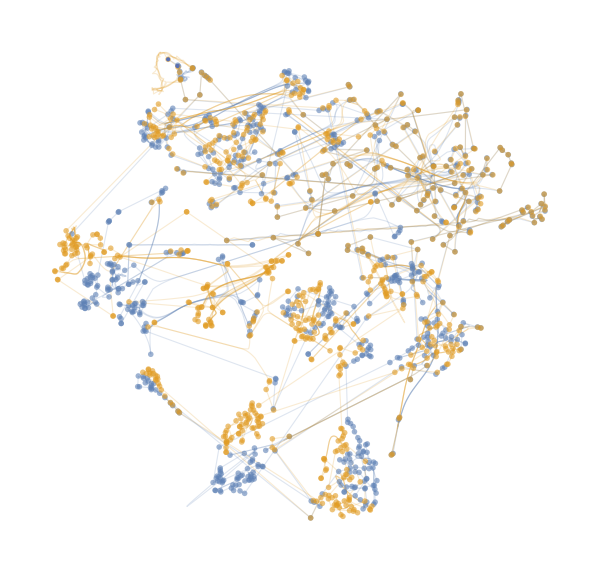

```mathematica
SetProperty[gr,{ImageSize->600
,GraphLayout->{"EdgeLayout"->{"DividedEdgeBundling","CoulombConstant"->1300,"VelocityDamping"->0.7,"SmoothEdge"->False}}
}
]
```